## Dunaew Viktar, 4 kurs, 6 group, Variant 604

## -Graphics-

#### X min = -1.5, X max = 1.5, Y min = 0, Y max = 5, Z min = -10, Z max = 10.

### Initialization data

```mathematica
xMin = -1.5;
xMax = 1.5;
yMin = 0.0;
yMax = 5.0;
zMin = -10.0;
zMax = 10.0;

xPla = xMin+1;
xInc = xPla+1;

zSlo = 5.0;
xLog = -0.5;
aSlo = 10.0;
```

### Pre_Task

```mathematica
zBasic[x_] := If[x <= xPla, zMin+5, If[x <= xInc, aSlo*x, 5*Log[x - xLog] + zSlo]];
```

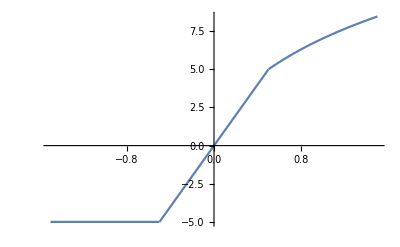

```mathematica
Plot[zBasic[x],{x,xMin,xMax}]
```

```mathematica
fOrigin[x_,y_] := zBasic[x];
```

### MY_Colors

```mathematica
myColors[z_] := Blend[{RGBColor[20/255,255/255,0],
					RGBColor[20/255,195/255,0],
					RGBColor[20/255,135/255,0],
					RGBColor[20/255,75/255,0],
					RGBColor[20/255,15/255,0]},z];
myColors[_, _, z_] := myColors[z];
```

## Task 1

```mathematica
Plot3D[zBasic[x],{x,xMin,xMax},{y,yMin,yMax},Exclusions->None,ColorFunction->myColors]
```

-Graphics3D-

## Task 2

```mathematica
fTrench[x_,y_] := If[-1≤x≤1 && -1≤y≤1,-1,0];
fPyramid[x_,y_] := If[-1≤x≤1 && -1≤y≤1,1-Max[Abs[x],Abs[y]],0];
fHill[x_,y_] := If[-1≤x≤1 && -1≤y≤1,Cos[(π*x)/2]*Cos[(π*y)/2],0];

fSurf[x_,y_] := fOrigin[x,y] + 5*fPyramid[4*(x-1),2*(y-1)] + 2*fTrench[4*(x-1),2*(y-3.5)] +
 4*fHill[4*(x+1),2*(y-3.5)] - 2*fHill[4*(x+1),2*(y-1.5)];
```

```mathematica
myPlot = Plot3D[fSurf[x,y],{x,xMin,xMax},{y,yMin,yMax},AxesLabel->Automatic,
Exclusions->None,BoxRatios->{2, 2, 1},ColorFunction->myColors]
```

-Graphics3D-

## Task 3

```mathematica
Plot[zBasic[x],{x,xMin,xMax}]
```

-Graphics-

```mathematica
Plot3D[zBasic[x],{x,xMin,xMax},{y,yMin,yMax},Exclusions->None,ColorFunction->myColors]
```

-Graphics3D-

```mathematica
myPlot = Plot3D[fSurf[x,y],{x,xMin,xMax},{y,yMin,yMax},AxesLabel->Automatic,
Exclusions->None,BoxRatios->{2, 2, 1},ColorFunction->myColors]
```

-Graphics3D-

## Task 4

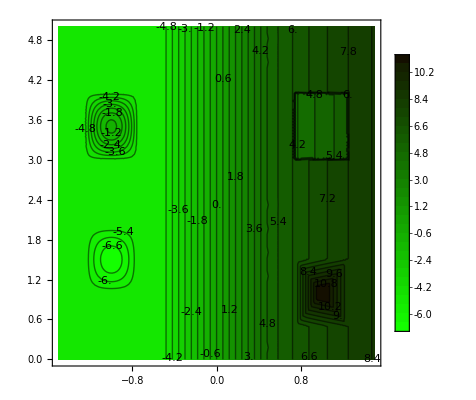

```mathematica
ContourPlot[fSurf[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic,Exclusions->None,ContourLabels->True,
Contours->30,ColorFunction->myColors]
```

```mathematica
myMesh = DiscretizeGraphics[myPlot,BoxRatios->{2, 2, 1}]
```

-Graphics3D-

```mathematica
meshData = MeshCoordinates[myMesh]//TableForm;
```

## Task 5

```mathematica
Manipulate[Grid[Plot[fSurf[x1+t(x2-x1),y1+t(y2-y1)],{t,0,1},Exclusions->None,ImageSize->Medium],
Show[Plot3D[fSurf[x,y],
		{x,xMin,xMax},{y,yMin,yMax},AxesLabel->Automatic,
		Exclusions->None,BoxRatios->{2, 2, 1},ColorFunction->myColors,ImageSize->Medium],
	Graphics3D[{Opacity[0.5],Red,InfinitePlane[{{x1,y1,0},{x2,y2,0},{x2,y2,1}}]}]
]],
{x1,xMin,xMax,Appearance -> "Labeled"},
{x2,xMin,xMax,Appearance -> "Labeled"},
{y1,yMin,yMax,Appearance -> "Labeled"},
{y2,yMin,yMax,Appearance -> "Labeled"}]
```

```mathematica
Export[NotebookDirectory[] <> "MeshData.xls",meshData,"XLS"]
```

C:\7_semestr\KSVE\3_ТЕСТ\MeshData.xls

```mathematica
profilesCount = 10;
pointsCount = 10;

xStep = (xMax - xMin)/(profilesCount-1);
yStep = (yMax - yMin)/(pointsCount-1);

pointsList = {};

For[i = 1 , i ≤ profilesCount, i++,
	For[g = 1 , g ≤ pointsCount, g++,
		AppendTo[pointsList,{i,g,xMin+(i-1)*xStep,
								yMin+(g-1)*yStep,
								fSurf[xMin+(i-1)*xStep,yMin+(g-1)*yStep]}]
	]
];
Export[NotebookDirectory[] <> "PointsAndProfiles1.xls",pointsList,"XLS"]
```

C:\7_semestr\KSVE\3_ТЕСТ\PointsAndProfiles1.xls

## Task 6

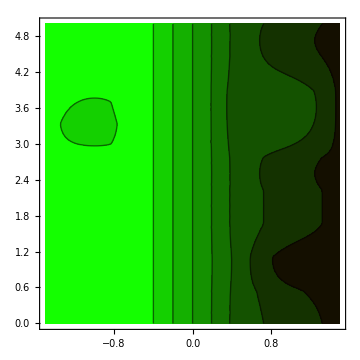
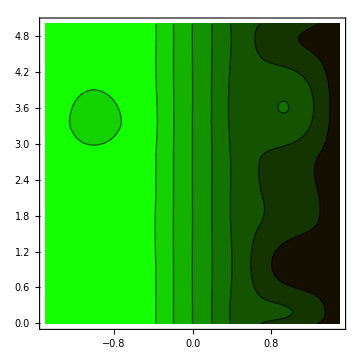
Grid[-Graphics-,-Graphics-]

```mathematica
interpolData = Table[{{x,y},fSurf[x,y]},{x,xMin,xMax,xStep},{y,yMin,yMax,yStep}];
interpolData = Flatten[interpolData,1];

interpolFunc2 = Interpolation[interpolData,InterpolationOrder->2];
interpolFunc5 = Interpolation[interpolData,InterpolationOrder->5];

Grid[ContourPlot[interpolFunc2[x,y],{x,xMin,xMax},{y,yMin,yMax},ImageSize->Medium,ContourStyle->Opacity[0.5],ColorFunction->myColors],
	ContourPlot[interpolFunc5[x,y],{x,xMin,xMax},{y,yMin,yMax},ImageSize->Medium,ColorFunction->myColors]]
```

## Task 7

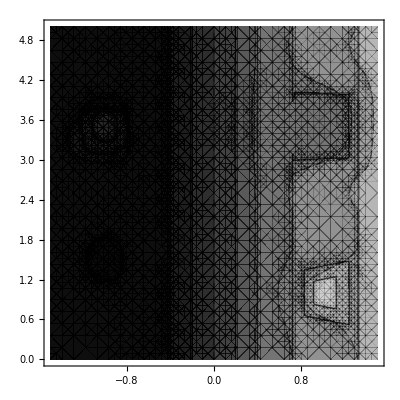

```mathematica
Show[ContourPlot[fSurf[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotTheme->"Monochrome",Exclusions->None],
ContourPlot[interpolFunc2[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotTheme->"Monochrome",ContourStyle->Dashed]]
```

## Task 8

InterpolatingFunction::dmval: Input value {-1.49979,0.000357143} lies outside the range of data in the interpolating function. Extrapolation will be used.

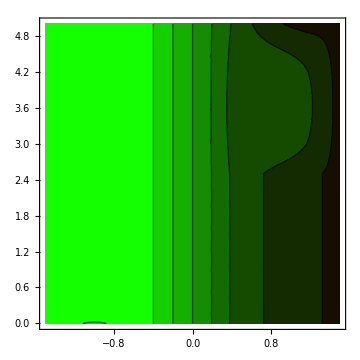
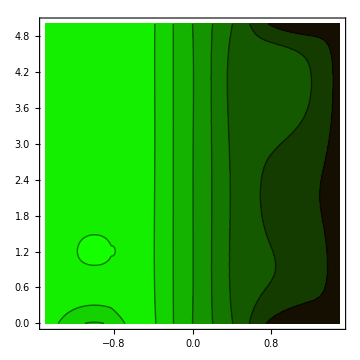
Grid[-Graphics-,-Graphics-]

```mathematica
pointsCount = 40;

xStep = (xMax - xMin)/(profilesCount-1);
massivY={0.5,1.75,2.5,4.0,4.75};
(* для увеличения точности постороения нужно увеличивать кол-во данных в massivY
   в данном случае берем только 5 переменных*)
pointsList = {};

For[i = 1 , i ≤ 5, i++,
	For[g = 1 , g ≤ pointsCount, g++,
		AppendTo[pointsList,{{xMin+(g-1)*xStep,
								massivY[[i]]},
								fSurf[xMin+(g-1)*xStep,massivY[[i]]]}]
	]
];
pointsList;

interpolData = pointsList;

interpolFunc2 = Interpolation[interpolData,InterpolationOrder->2];
interpolFunc5 = Interpolation[interpolData,InterpolationOrder->4];

Grid[ContourPlot[interpolFunc2[x,y],{x,xMin,xMax},{y,yMin,yMax},ImageSize->Medium,ContourStyle->Opacity[0.5],ColorFunction->myColors],
	ContourPlot[interpolFunc5[x,y],{x,xMin,xMax},{y,yMin,yMax},ImageSize->Medium,ColorFunction->myColors]]
```